```mathematica
T1[e13_,e23_]:=Catch[Module[{colc={e13,e23},mem={0,0}},
mem[[1]]=If[colc[[1]]≤1&&colc[[1]]≥0,colc[[1]],1/colc[[1]]];
mem[[2]]=If[colc[[2]]≤1&&colc[[2]]≥0,colc[[2]],1/colc[[2]]];
mem[[1]]=Mod[mem[[2]],mem[[1]]];
Throw[mem[[1]]];
]]
Px[x_]:=x-1/2 Floor[1/2 (-1+Sqrt[-7+8 x])] (1+Floor[1/2 (-1+Sqrt[-7+8 x])]);Py[x_]:=1/2 (2-2 x+Ceiling[1/2 (-1+Sqrt[1+8 x])]+Ceiling[1/2 (-1+Sqrt[1+8 x])]^2);
```

```mathematica
S1[err1_,err2_]:=Catch[Module[{colc1=err1,colc2=err2,mem={0,0,0},dat={},cnt={1,1}},
dat=colc1;
mem[[1]]=Length[dat];
mem[[2]]=Length[colc2];

Label["ToGo"];
If[cnt[[2]]>mem[[2]],dat=DeleteCases[dat,0];dat=DeleteCases[dat,-1];dat=DeleteCases[dat,1];Throw[dat];];
mem[[3]]=Mod[dat[[cnt[[1]]]],colc2[[cnt[[2]]]]];
If[dat[[cnt[[1]]]]≠0&&mem[[3]]==0,dat[[cnt[[1]]]]=0;Goto["ToGo2"];,cnt[[1]]++;Goto["ToGo"];];

Label["ToGo2"];
cnt[[1]]=cnt[[1]]+colc2[[cnt[[2]]]];
If[cnt[[1]]>mem[[1]],cnt[[1]]=1;cnt[[2]]++;Goto["ToGo"];,dat[[cnt[[1]]]]=0;Goto["ToGo2"];];
]];
```

```mathematica
Test[xx_,yy_,zz_,zz2_]:=Catch[Module[{colc={xx,yy,zz,zz2},mem},
If[colc[[4]]-colc[[2]]==0,Throw[0];];
mem=Floor[Mod[1/T1[colc[[1]],colc[[3]]],colc[[4]]-colc[[2]]]];
Throw[mem];
]];
FactInt[zzr_,zzr2_]:=Catch[Module[{colc=zzr,colc2=zzr2,mem={0,2,0,0,0,0,0,0},mem2,mem3={0,0,0},dat={},dat2={},cnt={0,0,1}},
mem2=Floor[Log[colc]^2];
mem[[3]]=Floor[(mem2 mem2/Floor[Log[mem2]]^2)/ⅇ];
mem[[5]]=Floor[ⅇ mem2];
mem3[[2]]=Floor[√colc];
mem3[[1]]=Floor[√mem3[[2]]];
dat=Table[Prime[the1],{the1,1,Floor[Log[mem[[3]]]/2]}];
mem[[7]]=Length[dat];

Label["GoGo"];
If[cnt[[1]]>mem2,Throw[{"Failed"}];];
mem[[1]]=Test[colc,mem[[5]]+cnt[[1]],mem3[[1]],mem3[[2]]];
If[mem[[1]]<colc2[[1]],cnt[[1]]++;Goto["GoGo"];];
If[mem[[1]]>colc2[[2]],cnt[[1]]++;Goto["GoGo"];];
mem[[6]]=mem[[1]]-mem[[3]];
mem[[8]]=mem[[1]]+mem[[3]];
cnt[[2]]=0;
cnt[[3]]=1;

Label["GoGo1a"];
dat2=Table[Mod[mem[[6]],dat[[yyet]]],{yyet,1,mem[[7]]}];

Label["GoGo1b"];
If[cnt[[3]]==mem[[7]] ,If[cnt[[2]]>mem[[8]],cnt[[1]]++;Goto["GoGo"];,Goto["GoGo2"];];];
If[cnt[[2]]==dat2[[cnt[[3]]]],dat2[[cnt[[3]]]]=dat[[cnt[[3]]]];cnt[[2]]++;cnt[[3]]=1;Goto["GoGo1b"];];
cnt[[3]]++;
Goto["GoGo1b"];

Label["GoGo2"];
mem[[4]]=Abs[mem[[6]]+cnt[[2]]];
If[mem[[4]]==1||mem[[4]]==0,cnt[[2]]++;Goto["GoGo1b"];];
mem[[4]]=Mod[colc,mem[[4]]];
If[mem[[4]]==0,Goto["GoGo3"];];
cnt[[2]]++;
If[cnt[[2]]≥2mem[[3]],cnt[[1]]++;Goto["GoGo"];];
Goto["GoGo1b"];

Label["GoGo3"];
Throw[Abs[mem[[6]]+cnt[[2]]]];
]];
```

```mathematica
$MaxExtraPrecision=10000;
```

```mathematica
memr=Prime[3000]Prime[4000];
```

```mathematica
DeleteCases[{2,0,2},0]
```

{2,2}

```mathematica
Floor[1.3^100]
```

```mathematica
Length[IntegerDigits[memr,2]]
```

59

```mathematica
Prime[200]
```

1223

```mathematica
Timing[Mod[NextPrime[10^350],Prime[200]]]
```

{0.277949,366}

```mathematica
Mod[40-17,23]
```

0

```mathematica
{Timing[FactInt[memr,{Floor[√(√memr)],Floor[√memr]}]],Timing[FactorInteger[memr]]}
```

{{1.09161,27449},{0.000604,{{27449,1},{37813,1}}}}

```mathematica
Prime[300000]
```

4256233

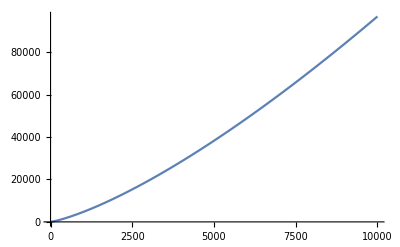

```mathematica
Plot[Pn[bn],{bn,1,10000}]
```

```mathematica
Timing[FactInt[Prime[2000]Prime[3000],{8000,40000}]]
```

{13.6015,17389}

```mathematica
Floor[1375/60]
```

```mathematica
50
```

```mathematica
5500 mins
```

5500 mins

```mathematica
Row[{1,IntegerDigits[Prime[3100000]Prime[2000000],2],22,IntegerDigits[Prime[31000000]Prime[20000000],2]}]
```

1{1,0,1,1,1,1,1,0,1,1,1,1,0,0,1,0,1,0,1,0,1,1,1,0,1,1,1,0,1,0,1,0,1,1,1,0,1,0,1,1,1,0,1,0,1,1,0,0,0,0,1}22{1,1,0,0,0,1,0,0,1,1,1,0,1,0,0,1,0,1,0,1,1,0,1,0,1,0,0,0,0,1,1,0,1,1,0,0,0,0,1,0,0,1,0,0,1,0,1,0,1,1,0,0,0,1,0,0,0,1}

```mathematica
Prime[20000000]
```

373587883

```mathematica
Test[mem,7]-Floor[Log[2,mem]]
```

1226

```mathematica
N[Log[2,Prime[20]Prime[300]]]
```

17.1061

```mathematica
{FactorInteger[915],Prime[20]}
```

{{{3,1},{5,1},{61,1}},71}